15

正交函数及其物理应用

在球坐标和柱坐标系，Helmholtz方程分离变量，得到微分方程，分别为

∇^2 w(r,θ,ϕ)+λ w(r,θ,ϕ)=0    →^(w(r,θ,ϕ)=R(r)Θ(θ) Φ(ϕ))

{Φ''+γ Φ=0
1/(sin θ)ⅆ/ⅆθ(sin θ Θ')+[l(l+1)-γ/(sin^2 θ)]Θ=0   (⟹_(x = cos θ))^(y(x) = Θ(θ))    ⅆ/ⅆx[(1-x^2)ⅆy/ⅆx]+[l(l+1)-m^2/(1-x^2)]y=0
ⅆ/ⅆr(r^2 R')+[λ r^2-l(l+1)]R=0

∇^2 w(ρ,ϕ,z)+λ w(ρ,ϕ,z)=0    →^(w(ρ,ϕ,z)=R(ρ)Φ(ϕ)Z(z))

{Z''+μ Z=0
Φ''+γ Φ=0
ρ^2 R''+ρ R'+[(λ-μ)ρ^2-γ]R=0

前面我们较为详细地讨论了两个蓝色的方程，分别对应于关联 Legendre 方程与Bessel方程。

其中紫色显示的是由边界条件或自然条件或周期条件确定的分离变量常数。

物理上的方程当然不局限于Helmholtz方程。其它方程类似地也会遇到一个

由边界条件或自然条件或周期条件来确定（分离变量）常数的常微分方程

这类方程的解有一些共同的特征：具有生成函数、递推关系、正交、完备、微分积分表示等等。

数学家们总喜欢归纳成一类数学问题，这就是 Sturm-Liouville 问题。

为此，在讨论其它正交函数之前，我们先讨论 Sturm-Liouville 问题及其解的一般性质。

## 15.1 Sturm-Liouville方程

我们遇到的经由分离变量得到的二阶常微分方程：

y''+μ y=0              来自一维、柱、球坐标分系离变量中的 Φ 或柱坐标分系离变量中的 Z
x^2 y''+x y'+[(λ-μ)x^2-γ]y=0          来自柱坐标系分离变量中的 R
ⅆ/ⅆx[(1-x^2)ⅆy/ⅆx]+[l(l+1)-m^2/(1-x^2)]y=0     来自球坐标系分离变量中的 Θ

有一个共同的特点： 零阶导数项的系数带一个分离变量常数

一般地，经由分离变量得到的二阶常微分方程总有以下形式：

f(x)y''+g(x)y'+h(x)y+λ w(x)y=0    其中 λ 为分离变量常数

数学上，将具有以下形式的常微分方程，称为 Sturm-Liouville 方程

ⅆ^/(ⅆ x_)[p(x)ⅆy/ⅆx]-q(x)y+λ w(x)y=0         ——  Sturm-Liouville 方程

其中：λ 为待定常数（分离变量常数）

函数 y(x) 定义于 a≤x≤b 并且在端点 a,b 满足某种边条（Sturm-Liouville 边条，以下会讨论）

由边条确定常数 λ 的允许取值（以避免微分方程仅有平庸解，即 0 解）

那么，是否任意由分离变量得到的常微分方程：f(x)y''+g(x)y'+h(x)y+λ w(x)y=0

均可写成 Sturm-Liouville 方程：ⅆ/ⅆx[p(x)ⅆy/ⅆx]-q(x)y+λ w(x)y=0？

回答是肯定的。先看几个例子。

例 1.  Legendre方程

ⅆ/ⅆx[(1-x^2)ⅆy/ⅆx]+l(l+1)y=0

该方程显然是Sturm-Liouville 方程的特殊情况，相当于Sturm-Liouville 方程中

p(x)=1-x^2,  q(x)=0,   w(x)=1,  λ=l(l+1)

例 2.  Bessel方程

x^2 y''+x y+(x^2-m^2)y=0     ⟹    ⅆ/ⅆx[x ⅆy/ⅆx]+(x-m^2/x)y=0

好像属Sturm-Liouville 方程，怎么没有“分离变量”常数？（m 不由此方程确定）

再回头看该方程从分离变量中得到的原始形式：

ρ^2 R''+ρ R'+[(λ-μ)_(⏟_(α^2))ρ^2-m^2]R=0    ⟹   ⅆ/ⅆρ[ρ ⅆR/ⅆρ]+(α^2 ρ-m^2/ρ)R=0

比较Sturm-Liouville 方程：ⅆ/ⅆx[p(x)ⅆy/ⅆx]-q(x)y+λ w(x)y=0

原来对应于：p(x)=x,  q(x)=m^2/x,   w(x)=x,  λ=α^2    果然逃不过Sturm-Liouville

物理上的许多问题，都可以化为 Sturm-Liouville 方程：ⅆ/ⅆx[p(x)ⅆy/ⅆx]-q(x)y+λ w(x)y=0。

或者说，形如 f(x)y''+g(x)y+h(x)y+λ w(x)y=0 的方程，均可化为 Sturm-Liouville 方程。（证明见下）

为简化起见，把 Sturm-Liouville 方程改写成：

ℒ|y⟩=-λ w|y⟩,          其中：ℒ=ⅆ/ⅆx[p(x)ⅆ/ⅆx]-q(x)  是个算符。

这种形式看起来似乎很清爽，特像量子力学。特别是将函数 y(x) 写成 |y⟩ 形式。

这个形式看起来怎么有点眼熟，试着令 w=-1 看看：ℒ|y⟩=λ |y⟩  —— 原来是个本征值问题。

这就对了，我们已把Sturm-Liouville 方程写成：广义（w≠-1）本征值问题的形式

—— 怪不得我们把它称为微分方程的本征值问题。

因此，对以上一些表述，我们整理出以下几个问题：

形如 f(x)y''+g(x)y'+h(x)y+λ w(x)y=0 的方程，是否均可化为 Sturm-Liouville方程?

ⅆ^/(ⅆ x_)[p(x)ⅆy/ⅆx]-q(x)y+λ w(x)y=0

Sturm-Liouville方程：ℒ|y⟩=-λ w|y⟩ 在什么条件下可以确定分离变量常数 λ

确定了分离变量常数后得到的一系列解，是否构成一个正交完备基，

使得满足一定条件的函数均可以这一套基函数展开？

人们把求解分离变量常数 λ 的过程，称为求解本征值，这与线性代数中的求解本征值有何关系。

以下，我们分别回答这些问题。

### 先回答第四个问题。微分方程的本征值问题与线性代数的本征值问题之间的关系。

假设有一套基函数 ϕ_i(x)，i=1,2,… N，满足正交特性：∫_a^b ϕ_i(x) ϕ_i(x)w(x)ⅆx=δ_(i j)

——  可以用“Gram-Schmidt 正交归一方法”构造  ϕ_i(x)

并且使得函数 y(x) 可以按这套正交完备基函数展开：y(x)=(∑_(j=1))^N y_j ϕ_j(x)，y_j 为常数

那么，微分方程的本征值问题   ⅆ/ⅆx[p(x)ⅆy/ⅆx]-q(x)y=-λ w(x)y    就可化为：

(∑_(j=1))^N {ⅆ/ⅆx[p(x)ⅆ/ⅆx]-q(x)}y_j ϕ_j(x)=-λ(∑_(j=1))^N  w(x) y_j ϕ_j(x)

两边同乘以 ϕ_i(x) 并对 x 从 a 到 b 积分，利用正交性：∫_a^b ϕ_i(x) ϕ_i(x)w(x)ⅆx=δ_(i j)

得：   (∑_(j=1))^N y_j(∫_a^b ϕ_i(x){ⅆ/ⅆx[p(x)ⅆ/ⅆx]-q(x)}ϕ_j(x)ⅆx)_(⏟_(ℒ_(i j)))=-λ y_i

即：ℒ_(i j) y_j=-λ y_i     其中 ℒ_(i j) 为 N×N 矩阵，显然，这是一个矩阵本征值问题。

因此，对第 4 个问题的回答是，只要找到一套正交完备基，则微分方程本征值问题等同于矩阵本征值问题。

微分方程本征值问题与矩阵本征值问题通过一套正交完备基联系起来。

### 再回答第一个问题 一般二阶常微分方程化为Sturm-Liouville方程

Sturm-Liouville 方程具有以下形式

ⅆ/ⅆx[p(x)ⅆy/ⅆx]-q(x)y+λ w(x)y=0

故：

Legendre 方程：ⅆ/ⅆx[(1-x^2)ⅆy/ⅆx]+l(l+1)y=0
Bessel 方程：ⅆ/ⅆρ[ρ ⅆR/ⅆρ]+(α^2 ρ-m^2/ρ)R=0}  均可视为其特例

Sturm-Liouville 方程的形式是

p(x)y''+p'(x)y'-q(x)y+λ w(x)y=0

二阶导数项的系数：p(x)      而一阶导数项的系数：p'(x)

一般分离变量得到的二阶线性常微分方程总可以写成如下形式：

f(x)(ⅆ^2 y)/(ⅆ x^2)+g(x)ⅆy/ⅆx+h(x)y=-λ w̃(x)y         分离变量常数不出现在导数项的系数中

为方便比较，将两个方程的二阶导数的系数化为 1，得：

{y''+(p'(x))/(p(x))y'-(q(x))/(p(x))y=-λ (w(x))/(p(x))y             Sturm-Liouville 形式
y''+(g(x))/(f(x))y'+(h(x))/(f(x))y=-λ (w̃(x))/(f(x))y             一般分离变量得到的二阶线性常微分方程

重要的差异在于一阶导数 y^′的系数 （蓝色部分），因而

令：(g(x))/(f(x))=(p'(x))/(p(x))      ⟹^两边同时积分     ln p(x)=∫(g(x))/(f(x))ⅆx

⟹   p(x)=exp[∫(g(x))/(f(x))ⅆx]

求出 p(x)，则二阶、一阶导数项系数均相等，接着，令

{(h(x))/(f(x))=-(q(x))/(p(x))       ⟹       q(x)=-(h(x))/(f(x)) p(x)
(w̃(x))/(f(x))=(w(x))/(p(x))           ⟹      w(x)=-(w̃(x))/(f(x)) p(x)

经以上三个紫色公式，就把一般分离变量得到的二阶线性常微分方程：

f(x)(ⅆ^2 y)/(ⅆ x^2)+g(x)ⅆy/ⅆx+h(x)y=-λ w̃(x)y

写成Sturm-Liouville 形式：p(x)y''+p'(x)y'-q(x)y+λ w(x)y=0

#### 算符形式：

把分离变量得到的二阶线性常微分方程写成算符形式：

ℒ'|y⟩=-λ w(x) |y⟩,      ℒ'=f(x)ⅆ^2/(ⅆ x^2)+g(x)ⅆ/ⅆx+h(x)

应把 ℒ'=f(x)ⅆ^2/(ⅆ x^2)+g(x)ⅆ/ⅆx+h(x)  化为：ℒ=p(x)ⅆ^2/(ⅆ x^2)+p'(x)ⅆ/ⅆx-q(x) 形式。

比较：{(ⅆ^2 y)/(ⅆ x^2)+(g(x))/(f(x))ⅆy/ⅆx+(h(x))/(f(x))y=-λ (w(x))/(f(x))y       一般分离变量所得的二阶线性常微分方程
(ⅆ^2 y)/(ⅆ x^2)+(p'(x))/(p(x))ⅆy/ⅆx-(q(x))/(p(x))y=-λ (w(x))/(p(x))y        Sturm-Liouville 方程

重要的差异在于一阶导数的系数（蓝色部分），因而

令：(g(x))/(f(x))=(p'(x))/(p(x))      ⟹^两边同时积分     ln p(x)=∫(g(x))/(f(x))ⅆx    ⟹   p(x)=exp[∫(g(x))/(f(x))ⅆx]

算符ℒ'=f(x)ⅆ^2/(ⅆ x^2)+g(x)ⅆ/ⅆx+h(x) 应该使二阶导数的系数为 p(x)，为此，

左乘函数：F(x)=(p(x))/(f(x))=exp[∫(g(x))/(f(x))ⅆx]/(f(x))     （注意 当 g(x)=f'(x)时 F(x)=1）

故：F(x)ℒ'=exp[∫(g(x))/(f(x))ⅆx]ⅆ^2/(ⅆ x^2)+ exp[∫(g(x))/(f(x))ⅆx](g(x))/(f(x))ⅆ/ⅆx+F(x)h(x)

F(x)ℒ' 算符中一阶导数项的系数（紫色部分）刚好是二阶导数项的系数（蓝色部分）的导数！

F(x)ℒ'=ⅆ/ⅆx[exp[∫(g(x))/(f(x))ⅆx]ⅆ/ⅆx]+F(x)h(x)

此即 Sturm-Liouville算符。也即，一般分离变量所得的二阶线性常微分方程可写成 Sturm-Liouville 形式

### 最后回答第二、第三个问题 Sturm-Liouville 方程的形式

满足

ℒ|y_m⟩=-λ_m w|y_m⟩

的非平庸函数 |y_m⟩=y_m(x) 称为Sturm-Liouville本征值问题中对应于本征值 λ_m 的本证函数。

现在，我们就可证明在一定条件下，Sturm-Liouville 方程对应于不同本征值的本证函数正交。

∫_a^b y_m(x)y_n(x)w(x)ⅆx=0      if  λ_m≠λ_n

证明：出发点，当然是Sturm-Liouville方程

ℒ|y_m⟩=-λ_m w|y_m⟩

⟹  {ⅆ/ⅆx[p(x)(ⅆ y_m)/ⅆx]-q(x)y_m+λ_m w(x)y_m=0               (1)
ⅆ/ⅆx[p(x)(ⅆ y_n)/ⅆx]-q(x)y_n+λ_n w(x)y_n=0                   (2)

(1)×_(y^)_n-(2)×y_m 得：（这种做法在证明Legendre多项式或Bessel函数正交时常用）

y_n ⅆ/ⅆx[p(x)(ⅆ y_m)/ⅆx]-y_m ⅆ/ⅆx[p(x)(ⅆ y_n)/ⅆx]=-(λ_m-λ_n) w(x)y_m y_n

两边同时积分，并利用分部积分：

∫_a^b y_n ⅆ/ⅆx[p(x)(ⅆ y_m)/ⅆx]ⅆx=[y_n p(x)(ⅆ y_m)/ⅆx]_a^b-∫_a^b p(x)(ⅆ y_n)/ⅆx(ⅆ y_m)/ⅆx ⅆx

得：[y_n p(x)(ⅆ y_m)/ⅆx-y_m p(x)(ⅆ y_n)/ⅆx]_a^b=-(λ_m-λ_n) ∫_a^b w(x)y_m y_n ⅆx

如果 y_n, y_m 满足适当的边界条件（上式左边为 0），则有：

∫_a^b w(x)y_m y_n ⅆx=0           ——  Sturm-Liouville 算符不同本征值的本证函数正交

其中：w(x) 称为权函数

那么，什么条件才能保证上式中紫色部分为 0？

[p(x)(y_n(ⅆ y_m)/ⅆx-y_m(ⅆ y_n)/ⅆx)]_a^b=0   ？？—— Sturm–Liouville 边条

也即确保 Sturm-Liouville 算符不同本征值的本证函数正交？

最简单的，是问题在两端点 a, b 满足以下三者之一：

y(a)=y(b)=0                                                           Dirichlet  齐次边条

y'(a)=y'(b)=0                                                       Neumann 齐次边条

y(a)+α y'(a)=y(b)+β y'(b)=0                 Robin 齐次边条

证明

这三类齐次边条可写成：{α_1 y_m(a)+α_2 y'_m(a)=0
α_1 y_n(a)+α_2 y'_n(a)=0

这是一个关于 (α_1,α_2) 的二元一次方程组，α_1, α_2 不同时为 0

(故：|y_m(a)   y'_m(a)
y_n(a)   y'_n(a)|=0   ⟹  (y_n y'_m-y_m y'_n)|)_(x=a)=0    满足 Sturm–Liouville 边条

当然，周期边条也行：

{y(a)=y(b)
y'(a)=y'(b)   且 p(a)=p(b)

“还有还有，那梦中的橄榄树”：自然边条

当 p^(a)=p^(b)=0时， x=a, b 是Sturm-Liouville 方程：

ⅆ/ⅆx[p(x)ⅆy/ⅆx]-q(x)y+λ w(x)y=0   ⟹  y''+(p'(x))/(p(x))y'-[q(x)-λ w(x)]/(p(x))y=0

的奇点—— 不能保证方程的解 y(x) 在端点一定有限（级数在 a, b 发散）

因此需要自然边界条件才能确定本征值。Legendre方程就属此类。

即：p^(a)=p^(b)=0 时往往需要自然边界条件才能确定本征值。

通常，若 a, b 为有限，由以上这些边界条件确定的本征值构成半无限的可数集合。

可数集合：集合中的元素能与正整数或正整数的一个子集建立一一对应关系。

有限个元素的集合一定是可数集合，有理数构成的集合也是可数集合。

形象一点（不那么严谨）地说：就是本征值是分立的。

如Legendre方程中 l 取正整数，又如 Bessel方程中取 Bessel函数的根（也是分立的）。

数学上还可以证明：

Sturm-Liouville 算符构成区域 a≤x≤b 内分段连续函数 f(x) 正交完备归一的基函数，即：

f(x)=∑_(n=0)^∞ c_n y_n(x),     c_n=∫_a^b f(t)y_n(t)ⅆt

级数：∑_(n=0)^∞ c_n y_n(x)  平均值收敛于 f(x)，即满足：

lim_(N→∞) ∫_a^b (|f(x)-∑_(n=0)^N c_n y_n(x)|)^2 ⅆx=0

换言之，f(x)≠∑_(n=0)^∞ c_n y_n(x)  的点构成的集合的测度为 0

关于测度的讨论：∫_a^b (|f(x)|)^2 ⅆx=0  是否等价于 f(x)=0?

假设函数 f(x) 定义于闭区间 [0,1]，f(x)={1         当 x 为有理数时 
0          当 x 为无理数时

显然，f(x) 不恒等于 0

∫_0^1 f(x)ⅆx=?

Rieman 积分：不存在

上积分：OverBar[∫]f(x)ⅆx=∑_k Δx_i max[f(x)]       x_i≤x≤x_i+Δx_i
=1

下积分：UnderBar[∫]f(x)ⅆx=∑_k Δx_i min[f(x)]       x_i≤x≤x_i+Δx_i
=0

上下积分不相等，积分不存在。

Lebesgue 积分：存在，积分值为 0，因为 f(x)≠0的点构成的集合的测度为 0。

既然 f(x)仅在有理数上为 1，就可以按以下做法，将这些函数值不为 0 的点都覆盖住

任取一个宽度为 ε 的小纸片，对第一个 f(x)≠0的点撕下一半盖住，

再撕一半盖住第二个 f(x)≠0的点，可以一直做下去，盖住所有 f(x)≠0的可数点集

如此，我们只用一张宽度为 ε 的小纸片，盖住了所有 f(x)≠0 的点。

而这张小纸片的宽度 ε 可以任意小，因此其测度为 0。

因此 Lebesgue 积分为 0。

综上：lim_(N→∞) ∫_a^b (|f(x)-∑_(n=0)^N c_n y_n(x)|)^2 ⅆx=0  表明

f(x)=∑_(n=0)^∞ c_n y_n(x) 并非在 a≤x≤b 区间上的每一点都成立，但 f(x)≠∑_(n=0)^∞ c_n y_n(x) 的点集测度为 0 。

### Sturm-Liouville 算符的其它性质：自伴性质，本征值正定性质

若实函数，|u⟩, |v⟩ 满足Sturm–Liouville 边条：

[p(x) v ⅆu/ⅆx-p(x) u ⅆv/ⅆx]_a^b=0

定义两函数的内积为：

⟨u|v⟩≡∫_a^b u(x) v(x)ⅆx

观察：⟨u|ℒ|v⟩，注意这里算符作用于它右边的函数且 ℒ=ⅆ/ⅆx[p(x)ⅆ/ⅆx]-q(x)

⟨u|ℒ|v⟩≡∫_a^b u(x) ℒ v(x)ⅆx=∫_a^b u(x) ⅆ/ⅆx[p(x)(ⅆv(x))/ⅆx]ⅆx-∫_a^b u(x) q(x)v(x)ⅆx
=-([p(x)v ⅆu/ⅆx-p(x)u ⅆv/ⅆx ]_a^b)_(⏟_(Sturm–Liouville 边条))+∫_a^b v(x) ⅆ/ⅆx[p(x)(ⅆu(x))/ⅆx]ⅆx-∫_a^b v(x) q(x)u(x)ⅆx
=∫_a^b v(x) ℒ u(x)ⅆx=⟨v|ℒ|u⟩

故：Sturm–Liouville算符 ℒ 是自伴的 (self-adjoint)，称为自伴算符

若 |u⟩, |v⟩  为复函数，定义内积：

⟨u|v⟩≡∫_a^b u^*(x) v(x)ⅆx

若复算符 ℋ 满足

⟨u|ℋ|v⟩=[⟨v|ℋ|u⟩]^*   即：∫_a^b u^*(x) ℋ v(x)ⅆx=∫_a^b v(x) ℋ^* u^*(x)ⅆx

则称算符ℋ 是厄米算符。

实函数的自伴算符是厄米算符的特殊形式。因而厄米算符的性质，自伴算符也都满足。

数学上可以证明：厄米算符，有以下性质

本征值都是实的

不同本征值的本证函数正交

本证函数构成完备基函数

这些性质与厄米矩阵的性质类似，只不过厄米算符相当于无穷阶的厄米矩阵

因而，我们有以下结论：

对实函数，Sturm-Liouville算符满足上述三个性质。

自伴算符相当于无穷阶的实对称矩阵，因为基函数是无穷维的。

自伴算符是厄米算符的特殊形式，正如 实对称矩阵是厄米矩阵的特殊形式

除了厄米算符的三个重要性质外，Sturm-Liouville算符还有一重要性质，即：

4. 若p(x), q(x), w(x) 在区间[a,b] 均为非负，则本征值必为非负。

证明

对本证函数 y_n，有

ℒ|y_n⟩=-λ_nw|y_n⟩   ⟹   ⅆ/ⅆx[p(x)(ⅆ y_n)/ⅆx]-q(x)y_n+λ_n w(x)y_n=0

两边乘 y_n 并积分，得：

I=λ_n∫_a^b w(x)y_n^2 ⅆx=∫_a^b q(x)y_n^2 ⅆx -∫_a^b y_n ⅆ/ⅆx[p(x)(ⅆ y_n)/ⅆx]ⅆx
(第二项分部积分=-p_(x)y_n y'_n|)_a^b+∫_a^b p(x)y'_n^2 ⅆx

I=∫_a^b q(x)y_n^2 ⅆx+∫_a^b p(x)y'_n^2 ⅆx+p(a)y_n(a)y'_n(a)-p(b)y_n(b)y'_n(b)
≥p^(a)y_n(a)y'_n(a)-p(b)y_n(b)y'_n(b)=J   即 ：I≥J

对周期边条、自然边条_(⏟_(p(a)=p(b)=0))和第一、第二类齐次边条，易证：J=0

对第三类齐次边条：{α y_n(a)+y'_n(a)=0
β y_n(b)+ y'_n(b)=0    ⟹  {y'_n(a)=-α y_n(a)
y'_n(b)=-β y_n(b)

第三类齐次边条的特性：β>0,  α<0

J=-α p(a) y_n^2(a)+β p(b) y_n^2(b)>0

故：总有 I ≥J≥0，即：λ_n∫_a^b w(x)y_n^2 ⅆx≥0   ⟹  λ_n≥0

最后，对“分离变量得到常微分方程，进而得到特殊函数”的过程，我们都试着用同一个思路理解。

—— 特殊函数那些事：

微分方程 | 级数解   | 典型图形 |  生成函数 | 递推关系 | 微分积分表示 | 正交完备 | x→∞ 渐近行为       |            加法定理
↕          | ↕         | ↕          | ↕          | ↕          | ↕               | ↕           | ↕                       |                    ↕        
家庭背景 | 个人形象 | 几张小照 | 父母       | 朋友闺蜜 | 衣着打扮      | 个人品德
三从四德 |           “一起慢慢变老”
     “执子之手与子偕老”  |       “身许家国，心许你。”
               身心分离？

## 15.2 Hermite 多项式：一维谐振子

### Hermite 微分方程

y''-2x y'+2m y=0

“卿本佳人，奈何做贼”，如此简单的微分方程，偏偏就不是Sturm-Liouville形式。

当然，乘以：F(x)=(p(x))/(f(x))=exp[∫(g(x))/(f(x))ⅆx]/(f(x))=ⅇ^(-x^2) 就是了：

ⅆ/ⅆx[ⅇ^(-x^2)(ⅆ y)/ⅆx]+2m ⅇ^(-x^2)y=0

函数定义于：-∞<x<+∞    （无界区域）

### 级数解

x=0 是微分方程的常点，据  Frobenius and Fuchs 定理 ，方程必有以下形式的解：

y(x)=(∑_(k=0))^∞c_k x^k

带入微分方程的系数的递推关系

c_(k+2)=-(2(m-k))/((k+1)(k+2))c_k

两个线性独立解，分别对应于偶次幂与奇次幂，给定 c_0,   c_1 即可得两解。

当 m 为整数时，其中一个解退化为多项式。

m 为偶数时，取  c_0=((-1)^(m/2)m!)/((m/2)!)， m 为奇数时，取  c_1=((-1)^((m-1)/2)2m!)/([(m-1)/2]!)

得同一个表达式：（m≥0）

H_m=(∑_(k=0))^⌊m/2⌋(-1)^k(m!)/(k!(m-2k)!)(2x)^(m-2k)        注意其奇、偶幂次的特性

其中    ⌊m/2⌋ =Piecewise[{{m/2, m  even}, {(m-1)/2, m  odd}}]

### 图形

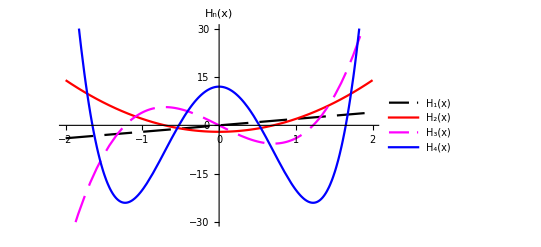
H_0(x)=1     
H_1(x)=2x
H_2(x)=4 x^2-2
H_3(x)=8 x^3-12
H_4(x)=16 x^4-48 x^2+12          -Graphics-

### 生成函数

g(x,t)=ⅇ^(-t^2+2t x)=(∑_(n=0))^∞H_n(x)t^n/(n!)

由生成函数可得积分表示。

### 递推关系

生成函数对 t 求导，

H_(n+1)(x)=2x H_n(x)-2n H_(n-1)(x)

生成函数对 x 求导

H'_n(x)=2n H_(n-1)(x)

联立可得：

H_(n+1)(x)=2x H_n(x)- H'_n(x)

### 微分表示、积分表示

Rodrigue微分表示

H_n(x)=(-1)^n ⅇ^(x^2)ⅆ^n/(ⅆ x^n)(ⅇ^(-x^2))

Schlaefli 积分表示 （生成函数 Taylor 展开系数）

H_n(x)=(n!)/(2π ⅈ)∮ t^(-n-1)ⅇ^(t^2-2t x)ⅆt

### 正交完备

Hermite 方程

y''-2x y'+2m y=0

写成Sturm-Liouville形式

ⅆ/ⅆx[ⅇ^(-x^2)(ⅆ y)/ⅆx]+2m ⅇ^(-x^2)y=0

比较：ⅆ/ⅆx[p(x)ⅆy/ⅆx]-q(x)y+λ w(x)y=0

对应于：p(x)=ⅇ^(-x^2),  q(x)=0,  w(x)=2 ⅇ^(-x^2)

权函数：2 ⅇ^(-x^2)，正交关系

∫_(-∞)^∞ H_m(x)H_n(x)ⅇ^(-x^2)ⅆx=0        if m≠n

可以导出：

∫_(-∞)^∞ [H_n(x)]^2 ⅇ^(-x^2)ⅆx= 2^n n!√π

证明

由Rodrigue微分表示：H_n(x)=(-1)^n ⅇ^(x^2)ⅆ^n/(ⅆ x^n)(ⅇ^(-x^2))

I=∫_(-∞)^∞ [H_n(x)]^2 ⅇ^(-x^2)ⅆx
=(-1)^n∫_(-∞)^∞ H_n(x)ⅆ^n/(ⅆ x^n)(ⅇ^(-x^2))ⅆx         分部积分
(=(-1)^n H_n(x)ⅆ^(n-1)/(ⅆ x^(n-1))(ⅇ^(-x^2))|)_(-∞)^∞-(-1)^n∫_(-∞)^∞ (ⅆH_n(x))/ⅆx ⅆ^(n-1)/(ⅆ x^(n-1))(ⅇ^(-x^2))ⅆx
=(-1)^(n-1)∫_(-∞)^∞ (ⅆH_n(x))/ⅆx ⅆ^(n-1)/(ⅆ x^(n-1))(ⅇ^(-x^2))ⅆx  
=∫_(-∞)^∞ (ⅆ^n H_n(x))/(ⅆ x^n) ⅇ^(-x^2)ⅆx         利用   (ⅆ^n H_n(x))/(ⅆ x^n)=2^n n!
=2^n n!∫_(-∞)^∞ ⅇ^(-x^2)ⅆx=2^n n!√π

完备：

f(x)=(∑_(n=0))^∞a_n H_n(x),     a_n=1/(2^n n!√π)∫_(-∞)^∞ f(x)H_n(x)ⅇ^(-x^2)ⅆx

### 渐近行为

当 n=v 不是整数时，

H_v(x)=(∑_(k=0))^∞c_k x^k

带入微分方程的系数的递推关系

c_(k+2)=-(2(v-k))/((k+1)(k+2))c_k     ⟹   k 很大时      c_(k+2)∼2/(k+2)c_k=c_k/((k+2)/2)

k 很大时，c_k 有近似解：c_k∼c/((k/2)!)

x 很大时，级数 H_v(x)=(∑_(k=0))^∞c_k x^k 的行为由 k 很大时的项所决定，因此

H_v(x)=(∑_(k=0))^∞c_k x^k    ⟹^(x → ∞)    H_v(x) ∼(∑_(k 大))^∞c_k x^k ∼ (∑_(k 大))^∞c/((k/2)!)x^k∼ (∑_(m 大))^∞c/(m!)x^(2m)∼c ⅇ^(x^2)

知：

H_v(x) ∼ ⅇ^(x^2)            v 为非整数， x→∞ 时

### 应用举例：一维谐振子

量子力学中最简单的例子，除了无限深势阱之外，就是一维谐振子。

质量为 m 的粒子一维势场中运动，Schrödinger方程

-ℏ^2/(2m)ⅆ^2/(ⅆ z^2)ψ(z)+V(z)ψ(z)=E ψ(z)

其中：ψ(z) 为波函数，E 为粒子能量，V(z) 为一维势能，对谐振子

V(z)=1/2 m ω^2 z^2         相当于一弹簧的势能，ω 为特征频率。

显然，这是个Sturm-Liouville 问题：ⅆ/ⅆx[p(x)ⅆy/ⅆx]-q(x)y+λ w(x)y=0

需要确定能量本征值 E。先做变量代换，无量纲化，简化方程。

x=α z,   α=(m ω)/ℏ,     λ=(2E)/(ℏ ω)

Schrödinger方程化为：

ⅆ^2/(ⅆ x^2)ψ-x^2 ψ+λ ψ=0   ——   标准Sturm-Liouville 问题

但并非我们熟悉的方程。再做变换：ψ(x)=ⅇ^(-x^2/2)η(x)，新函数 η(x) 满足的方程为：

η''-2x η' +(λ-1) η=0
比较 Hermite 方程：y''-2x y'+2n y=0

可知，只有 λ-1=2n 且 n 为正整数时，η(x) 在 x→∞ 时才有限，

否则：η(x) ∼  ⅇ^(x^2)    ⟹    ψ(x)=ⅇ^(-x^2/2)η(x)∼ⅇ^(x^2/2)    在 x→∞ 时为无穷大，不合物理。

这里蕴含的物理是：量子波函数在无穷远处必须为 0。

由此，我们得到，一维量子谐振子，能量是量子化的：

E=(ℏ ω)/2 λ=(ℏ ω)/2(2n+1)=(n+1/2)ℏ ω

波函数：     ψ_n(x)=c_n ⅇ^(-x^2/2)η(x)=c_n ⅇ^(-x^2/2)H_n(x)

其中 c_n 为归一化常数，利用 ∫_(-∞)^∞ (|ψ_n(x)|)^2 ⅆx=1 确定。

波函数： ψ_n(x)=1/((2^n n!√π)^(1/2))ⅇ^(-x^2/2)H_n(x)

原来，量子化与Sturm-Liouville 本征值问题有着物理与数学的内在联系，

正如，测不准关系与Fourier变换有着内在联系一样。

求归一化常数 c_n

```mathematica
cn[n_]:=1/((2^n n! √π)^(1/2));
nn=3;
t=Integrate[Exp[-x^2] HermiteH[nn,x]^2,{x,-∞,∞}];
dn=t^(1/2);
cn[nn]dn
```

1

几个最低能量波函数：

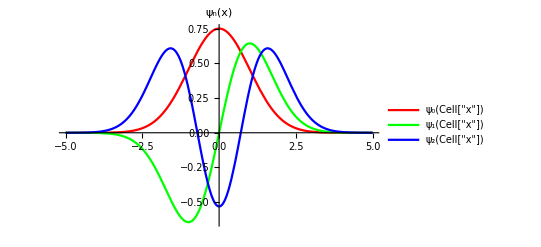

```mathematica
ψ[n_,x_]:=(ⅇ^(-x^2/2)HermiteH[n,x])/(2^(n/2)π^(1/4)(n!)^(1/2));
g2=Plot[{ψ[0,x],ψ[1,x],ψ[2,x]},{x,-5,5},PlotRange->All,
                 PlotStyle->{{Red},{Green},{Blue}},
                  PlotLabel->Style["ψ_n(x)",FontFamily->"Times",FontSize->20,FontSlant->Italic],
                  PlotLegends->{Style["ψ_0(Cell["x"])",FontFamily->"Times",FontSize->20,FontSlant->Italic],
            Style["ψ_1(Cell["x"])",FontFamily->"Times",FontSize->20,FontSlant->Italic],
             Style["ψ_2(Cell["x"])",FontFamily->"Times",FontSize->20,FontSlant->Italic]}]
```

注意，不同能级 n 的波函数，所对应的节点数不同，节点数等于 n。

波函数节点越多，对应的能量越高。

这一点：{在数学上， 可从 Sturm-Liouville 本征值问题加以论证
在物理上，可以理解为越是被压缩，能量越高。

## 15.3 Laguerre 函数：氢原子

### Laguerre 微分方程

x y''+(1-x) y'+n y=0

也不是Sturm-Liouville形式。

当然，乘以：F(x)=exp[∫(g(x))/(f(x))ⅆx]/(f(x))=ⅇ^-x 就变为是Sturm-Liouville形式了：

ⅆ/ⅆx[ⅇ^-x(ⅆ y)/ⅆx]+n ⅇ^-x y=0

函数定义于：0≤x<+∞

### 级数解

x=0 是微分方程的正则奇点，据  Frobenius and Fuchs 定理 ，方程必有以下形式的解：

y(x)=x^s(∑_(k=0))^∞c_k x^k,   c_0≠0,   s 称为指标

带入微分方程得指标方程：s^2=0

系数的递推关系

c_(k+1)=(k-n)/(k+1)^2 c_k

当 n 为正整数时，退化为多项式：—— Laguerre多项式

L_n(x)=(∑_(k=0))^n(-1)^k(n!)/((k!)^2(n-k)!)x^k

另一个线性无关解呢？

类似于Bessel方程，因为 x=0 是微分方程的正则奇点，

既然已经得到一个在 x=0 收敛（有限）的解，另一个解必然在 x=0 点发散。

所以在这里不深入讨论。

### 图形

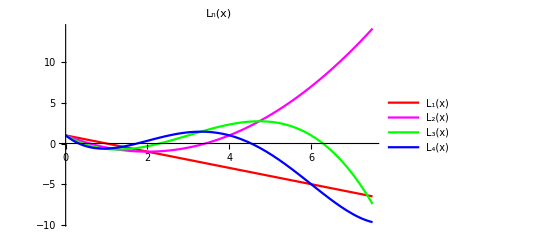
L_0(x)=1     
L_1(x)=-x+1
2!L_2(x)=x^2-4x+2
3!L_3(x)=−x^3+9 x^2−18x+6
4!L_4(x)=x^4−16 x^3+72 x^2−96x+24        -Graphics-

### 生成函数

g(x,t)=ⅇ^(-x t/(1-t))/(1-t)=(∑_(n=0))^∞L_n(x)t^n

由生成函数可得积分表示。

### 递推关系

生成函数对 t 求导，

(n+1)L_(n+1)(x)=(2n+1-x)L_n(x)-n L_(n-1)(x).

生成函数对 x 求导

L'_(n-1)(x)-L'_n(x)=L_(n-1)(x).

联立可得：

x L'_n(x)=n L_n(x)-n L_(n-1)(x)

### 微分表示、积分表示

Rodrigue微分表示

L_n(x)=ⅇ^x/(n!)ⅆ^n/(ⅆ x^n)(x^n ⅇ^-x)

Schlaefli 积分表示 （生成函数 Taylor 展开系数）

L_n(x)=(n!)/(2π ⅈ)∮ t^(-n-1)ⅇ^(-x t/(1-t))/(1-t)ⅆt

### 正交完备

Laguerre 方程

x y''+(1-x) y'+n y=0

写成Sturm-Liouville形式

ⅆ/ⅆx[ⅇ^-x(ⅆ y)/ⅆx]+n ⅇ^-x y=0

函数定义于：0≤x<+∞

比较：ⅆ/ⅆx[p(x)ⅆy/ⅆx]-q(x)y+λ w(x)y=0

对应于：p(x)=ⅇ^-x,  q(x)=0, 权函数： w(x)=ⅇ^-x

正交关系

∫_0^∞ L_m(x)L_n(x)ⅇ^-x ⅆx=δ_(m n)

完备：

f(x)=(∑_(n=0))^∞a_n L_n(x),     a_n=∫_0^∞ f(x)L_n(x)ⅇ^-x ⅆx

### 渐近行为

当 n=v 不是整数时，

L_v(x)=(∑_(k=0))^∞c_k x^k

带入微分方程的系数的递推关系

c_(k+1)=(k-n)/(k+1)^2 c_k

c_(k+1)=(k-v)/(k+1)^2 c_k     ⟹   k 很大时      (c_(k+1))/c_k∼1/(k+1)

比较：

ⅇ^x=(∑_(k=0))^∞x^k/(k!)=(∑_(k=0))^∞d_k x^(2k)      ⟹  k 很大时      (d_(k+1))/d_k∼1/(k+1)

知：

L_v(x) ∼ ⅇ^x            x→∞ 时

### 关联Laguerre函数

关联Laguerre函数

L_n^m(x)=(-1)^m ⅆ^m/(ⅆ x^m)L_(n+m)(x)

满足微分方程：

x y''+(m+1-x) y'+n y=0   —— the associated Laguerre equation
比较：x y''+(1-x) y'+n y=0           ——  the  Laguerre equation

Sturm-Liouville 形式

ⅆ/ⅆx[x^(m+1)ⅇ^-x ⅆy/ⅆx]+n x^m ⅇ^-x y=0

生成函数：

g(x,t)=ⅇ^(-x t/(1-t))/(1-t)^(m+1)=(∑_(n=0))^∞L_n^m(x)t^n

因为：  v 为非整数时，x→∞ 时，L_v(x) ∼ ⅇ^x，所以

v 为非整数时，x→∞ 时，L_v^m(x) ∼ ⅇ^x

除非，v = 正整数

### 应用举例：氢原子

量子力学中最简单的实际体系，氢原子问题。

质量为 μ 的电子在氢原子核的库仑势中运动，电子的波函数满足 Schrödinger方程

-ℏ^2/(2μ)∇^2 ψ(r⃗)+V(r⃗)ψ(r⃗)=E ψ(r⃗)

库仑势：V(r⃗)=-e^2/r    球对称势，这里用高斯单位制，没有 1/(4π ε_0)

Schrödinger 方程

-ℏ^2/(2μ)∇^2 ψ+V(r)ψ=E ψ，求电子能量 E 的可能取值即对应的电子波函数。

其中：ψ(r,θ,ϕ)为电子波函数，μ 为电子质量，ℏ=h/(2π), h 为 Plank 常数;

V(r)=-e^2/r   描述中心作用势能，E 是电子总能量（动能与势能之和）。

解：注意到 V(r) 与角度 (θ,ϕ) 无关，

对此类中心势场（球对称）问题，利用 ϕ 的周期条件以及 θ = 0, π 的有界条件，

可知角度函数为球谐函数：Y_l^m(θ,ϕ)

再利用：∇^2 =1/r^2∂/(∂r)(r^2∂/(∂r))-(L̂)^2/r^2       及    (L̂)^2 Y_l^m(θ,ϕ)=l(l+1)Y_l^m(θ,ϕ)

分离变量： ψ_(l m)=R_l(r)Y_l^m(θ,ϕ)  代入 Schrödinger 方程：-ℏ^2/(2μ)∇^2 ψ+V(r)ψ=E ψ

即可得径向波函数 R(r) 满足的常微分方程：

(1/r^2 ⅆ/ⅆr(r^2(ⅆ R_l)/ⅆr)-(l(l+1))/r^2 R_l)_(⏟_(除以角度函数  Y_l^m(θ,ϕ)的 ∇^2 ψ))+(2μ)/ℏ^2(e^2/r+E)R_l=0

引入：ρ=(-8μ E/ℏ^2)^(1/2)r        —— 无量纲化，ρ 是无量纲变量

方程变为：

(ⅆ^2 R_l)/(ⅆ ρ^2)+2/ρ(ⅆ R_l)/ⅆρ-(l(l+1))/ρ^2 R_l+(λ/ρ-1/4)R_l=0,

其中：λ=e^2/ℏ(μ/(2|E|))^(1/2)=(α((μ c^2)/(2|E|)))^(1/2)           ——  无量纲参数

α=e^2/(ℏ c) ∼ 1/137  —— 精细结构常数，无量纲参数

用点数学与“物理手段”化简。

看 ρ→∞ ， 略去 ∼1/ρ  及 ∼1/ρ^2 项，径向方程近似为：

u''-1/4 u=0  ⟶   u=a ⅇ^(ρ/2)+b ⅇ^(-ρ/2),  lim_(ρ→∞) ⅇ^ρ=∞,  不合物理，

故有：ρ→∞ 时  u(ρ)∼ ⅇ^(-ρ/2)

对较小的 ρ，令：R=ⅇ^(-ρ/2)u(ρ)，方程化为：

(ⅆ^2 u)/(ⅆ ρ^2)-(1-2/ρ)ⅆu/ⅆρ+((λ-1)/ρ-(l(l+1))/ρ^2)u=0,

再看 ρ→0  的情况，保留 ∼1/ρ^2 项，径向方程近似为：

u''+2/ρ u'-(l(l+1))/ρ^2 u=0      这里对一阶和二阶导数项均保留dominant项

⟹  ρ^2 u''+2ρ u'-l(l+1)u=0       ⟹^(§13.8 例 1)         u=a ρ^(-l-1)+b ρ^l,

第一项导致 R(ρ)=ⅇ^(-ρ/2)u(ρ)~ρ^(-l-1)在 ρ→0时发散，不合物理，  故有：ρ→0 时  u(ρ)∼ ρ^l

故，对一般的 ρ，设  u(ρ)=ρ^l v(ρ)，  记得： (R^)_(ρ)=ⅇ^(-ρ/2)u(ρ)=ρ^(l^)ⅇ^(-ρ/2)v(ρ)

记得 Plank在凑出黑体辐射公式时，也是从（低频与高频）两个极限出发哟，

可见这是个物理学家常用的“流氓手段”。

u(ρ)=ρ^l v(ρ)代入关于 u(ρ) 的径向方程：     (ⅆ^2 u)/(ⅆ ρ^2)-(1-2/ρ)ⅆu/ⅆρ+((λ-1)/ρ-(l(l+1))/ρ^2)u=0,

```mathematica
u[x_]=x^l v[x];
eq=D[u[x],{x,2}]-(1-2/x)D[u[x],x]+((λ-1)/x-(l(l+1))/x^2)u[x];
eq=Expand[eq];
c2=Coefficient[eq,v''[x]];
c1=Coefficient[eq,v'[x]];
c0=Coefficient[eq,v[x]];
c0=Simplify[c0/x^l];
c1=Simplify[c1/x^l];
c2=Simplify[c2/x^l];
eqs=c0 v[x]+c1 v'[x]+c2 v''[x];
FullSimplify[c0 v[x]+c1 v'[x]+c2 v''[x]-eq/x^l]
eqs//TraditionalForm
```

0

((2 l-x+2) v'(x))/x+((λ-l-1) v(x))/x+v''(x)

得 v(ρ) 满足的微分方程：

ρ v''+(2 l+2-ρ) v'+(λ- l-1) v=0               记得径向波函数： (R^)_(ρ)=ρ^(l^)ⅇ^(-ρ/2)v(ρ)

比较：x y''+(m'+1-x) y'+n' y=0   —— the associated Laguerre equation

得：{m'=2l+1
λ=n'+l+1

注意到 当 n' 不是 0 或正整数时，ρ→∞ 时，L_n'^m'(ρ) ∼ ⅇ^ρ    导致   R(ρ)=ρ^(l^)ⅇ^(-ρ/2)v(ρ)  →∞

故：    n' 为 0 或正整数  ⟹   λ=n'+l+1= n，  整数  n≥1

⟹    l=n-n'-1   即：l=0,1,..., n-1

电子能量：λ=e^2/ℏ(μ/(2|E|))^(1/2)=α((μ c^2)/(2|E|))^(1/2) =n

⟹     E=-1/2μ c^2 α^2/n^2              ——  此即量子力学中著名的 Bohr 公式

其中  n=1,2,…  称为主量子数，

一旦 n 确定，由于要求 l=n-n'-1 且 n' 为 0 或正整数，故：  l=0,1,…,n-1

上式的意义是：

电子能量不能取连续值，只能取分立值。源自波函数的边界条件。

从数学上看，能量取分立值来自Sturm-Liouville本征值问题中微分方程的本征值取分立值。

主量子数 n 与角动量量子数 l 满足：l≤n，即：给定 n，l=0,1,2,..., n-1

电子波函数：

注意到：{m'=2l+1
λ=n'+l+1=n       径向波函数：R(ρ)=ρ^l ⅇ^(-ρ/2)L_n'^m'(ρ)

ψ_(n l m)=c_(n l m) ρ^l ⅇ^(-ρ/2)L_(n-l-1)^(2l+1)(ρ)Y_(l m)(θ,ϕ)        c_(n l m)为归一化常数。

#### 另一种解法：

由径向方程 (1.EquationNumbered)

(ⅆ^2 R_l)/(ⅆ ρ^2)+2/ρ(ⅆ R_l)/ⅆρ-(l(l+1))/ρ^2 R_l+(λ/ρ-1/4)R_l=0,

其中：λ=e^2/ℏ(μ/(2|E|))^(1/2)=(α((μ c^2)/(2|E|)))^(1/2)           ——  无量纲参数

α=e^2/(ℏ c) ∼ 1/137  —— 精细结构常数，无量纲参数

直接利用 \[MathematicaIcon] Mathematica 求解

```mathematica
Clear["Global`*"]
eq=D[x^2 D[y[x],x],x]+(λ/x -1/4-(l(l+1))/x^2)x^2 y[x];
sol=DSolve[eq==0,y[x],x];
Simplify[sol,{l∈Integers,l≥0}]
```

{{y[x]→ⅇ^(-x/2) x^l (C[1] HypergeometricU[1+l-λ,2+2 l,x]+C[2] LaguerreL[-1-l+λ,1+2 l,x])}}

发现 associated  Laguerrel 函数，如果了解 Laguerre^ 函数，就可直接判断 α=(λ- l-1) 应该为自然数，

否则上述解中的 Laguerre函数项 在 x→ ∞ 时有渐近行为  ∼ ⅇ^x，必导致径向波函数在 x→ ∞ 时发散。

至于第一项，称为合流超几何函数 U(a,b,x)，当  a=(l+1-λ)=-α 不为负整数时，

上述解中的 合流超几何函数项 在 x→ 0 时有渐近行为  ∼ x^(-(2l+1))，必导致径向波函数在 x→ 0 时发散。

```mathematica
n0=2;
Series[HypergeometricU[-1,2 n0 +2,x],{x,0,2}]
Series[HypergeometricU[1,2 n0 +2,x],{x,0,0}]
```

-6+x+O[x]^3

24/x^5+24/x^4+12/x^3+4/x^2+1/x+O[x]^1